```mathematica
(*Definir el sistema de ecuaciones diferenciales*)sistema={P'[t]==-kon*P[t]*T[t]+koff*C0[t]+koff*C1[t],T'[t]==-kon*P[t]*T[t]+koff*C0[t]+koff*C1[t],C0'[t]==kon*P[t]*T[t]-(koff+kp)*C0[t],C1'[t]==kp*C0[t]-koff*C1[t],(*Condiciones iniciales*)P[0]==100,T[0]==20000,C0[0]==0,C1[0]==0};
```

```mathematica
(*Definir las constantes*)
kon=5*10^-5;
koff=0.01;
kp=1;
(*Definir el intervalo de tiempo*)
tmax=50;
```

```mathematica
(*Resolver el sistema de ecuaciones diferenciales*)
solucion=NDSolve[sistema,{P,T,C0,C1},{t,0,tmax}]
```

{{P→InterpolatingFunction[…],T→InterpolatingFunction[…],C0→InterpolatingFunction[…],C1→InterpolatingFunction[…]}}

```mathematica
(*Extraer la solución para y1(t)=C1(t)*)
y1[t_]:=C1[t]/. solucion[[1]];
```

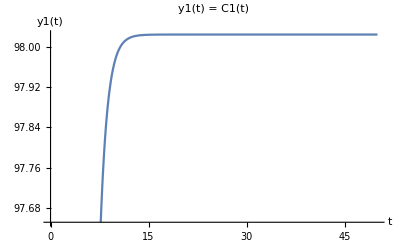

```mathematica
(*Graficar la solución y1(t)*)
Plot[y1[t],{t,0,tmax},PlotLabel->"y1(t) = C1(t)",AxesLabel->{"t","y1(t)"}]
```